#### Dimensionless, unamplified noise model

```mathematica
A= {{ λt,0},{1, -1}}
```

{{λt,0},{1,-1}}

```mathematica
X0={x0, y0}
```

{x0,y0}

```mathematica
Eigenvectors[A]
```

{{0,1},{1+λt,1}}

```mathematica
Eigenvalues[A]
```

{-1,λt}

```mathematica
MatrixExp[A*t].X0
```

{ⅇ^(t λt) x0,ⅇ^-t y0+(ⅇ^-t (-1+ⅇ^(t+t λt)) x0)/(1+λt)}

```mathematica
X[t_, x0_, y0_, λt_] = FullSimplify[%]
```

{ⅇ^(t λt) x0,(ⅇ^-t ((-1+ⅇ^(t+t λt)) x0+y0 (1+λt)))/(1+λt)}

```mathematica
Manipulate[Show[{ParametricPlot[X[t, x0, y0, λt], {t, 0, 1000}, PlotRange->2], Plot[{ 1}, {x, 0, 3}, PlotStyle->Dashed]}], {λt, 0.002, 0.2}, {x0, 0.5, 0.51}, {y0, 0.5, 0.51}]
```

#### Solve for the time y(t*)=1 and evaluate x(t*).

```mathematica
λs = {0.01, 0.02, 0.05, 0.1};
x0h = 0.8;
Δ=0.01;
varAndMeanFunc[λt0_, x0h_,Δ_]:=Module[{c, cf,y0h, x0Range, y0Range, params, tSolver, tvals, results, res,xpoints, grid, f},
c=1/(1+λt0);
cf = 1/(1+λ);
y0h =x0h*c;
x0Range = Table[p, {p, x0h-Δ, x0h+Δ, 0.0005}];
y0Range = Table[p, {p,y0h-Δ, y0h+Δ, 0.0005}];
params = Flatten[Table[{x0->x, y0->y, λt->λt0}, {x, x0Range}, {y, y0Range}], 1];
tSolver [params_]:=FindRoot[((ⅇ^-t ((-1+ⅇ^(t+t λt)) x0+y0 (1+λt)))/(1+λt)==1)/.params, {t,(1/λt)/.params}, AccuracyGoal->16, PrecisionGoal->16][[1]];
tvals = MapThread[tSolver, {params}];
results = Transpose[{params, tvals}];
res = Table[AppendTo[r[[1]], r[[2]]], {r, results}];
xpoints =Table[ⅇ^(t λt) x0/.p, {p, res}];
grid = Flatten[Table[{x,y}, {x, x0Range}, {y, y0Range}], 1];
f = Interpolation[Transpose[{grid, xpoints}]];
Return[{f, x0h, y0h, c}];]
```

```mathematica
results=Table[varAndMeanFunc[l, x0h, Δ], {l,λs}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

{{InterpolatingFunction[…],0.8,0.792079,0.990099},{InterpolatingFunction[…],0.8,0.784314,0.980392},{InterpolatingFunction[…],0.8,0.761905,0.952381},{InterpolatingFunction[…],0.8,0.727273,0.909091}}

```mathematica
{f, x0h, y0h, c} = results[[2]]
```

{InterpolatingFunction[…],0.8,0.784314,0.980392}

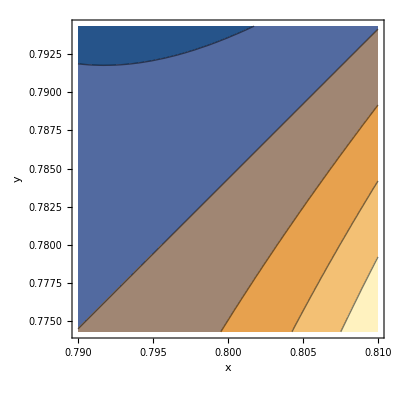

```mathematica
ContourPlot[f[x,y], {x,x0h-Δ, x0h+Δ}, {y, y0h-Δ, y0h+Δ}, AxesLabel->{"x", "y"}]
```

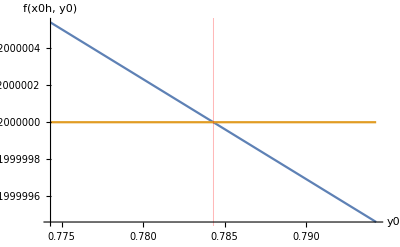

```mathematica
Show[{Plot[{f[x0h, y], 1/c},  {y, y0h-Δ, y0h+Δ}, AxesLabel->{"y0", "f(x0h, y0)"}, GridLines-> {{{y0h,Red}},None}]}]
```

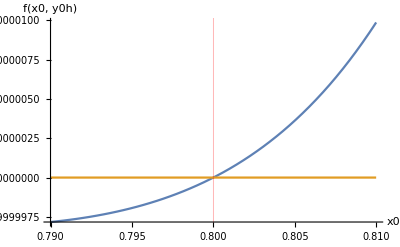

```mathematica
Plot[{f[x, y0h],1/c},  {x, x0h-Δ, x0h+Δ}, AxesLabel->{"x0", "f(x0, y0h)"}, GridLines-> {{{x0h,Red}},None}]
```

```mathematica
dFunction[f_,x0h_, y0h_, sigmaX_, sigmaY_]:=Module[{hess, fyy, fxx, fy, fx, fval},
hess = ({{D[f[x, y], {x,2}],D[f[x, y], x,y]},{D[f[x, y], x,y],D[f[x, y], {y,2}]}})/.{x->x0h, y->y0h};
fyy = hess[[2,2]];
fxx = hess[[1,1]];
fy = D[f[x, y], {y}]/.{x->x0h, y->y0h};
fx = D[f[x, y], {x}]/.{x->x0h, y->y0h};
fval = f[x, y]/.{x->x0h, y->y0h};
Return[{ sigmaY^2 fy^2,fval+sigmaY^2 fyy/2, sigmaX^2 fx^2, fval+sigmaX^2 fxx/2 }];]
```

#### width and mean with sy, lambda

```mathematica
MapThread[dFunction,{Transpose[results][[1]], Transpose[results][[2]], Transpose[results][[3]], Table[sx, 4],Table[sy, 4]}]
```

{{5.85705×10^-21 sy^2,1.01+2.66454×10^-9 sy^2,5.35834×10^-21 sx^2,1.01+1.28786×10^-8 sx^2},{2.92538×10^-11 sy^2,1.02-8.8818×10^-10 sy^2,2.81183×10^-11 sx^2,1.02+0.000331466 sx^2},{0.0000208164 sy^2,1.05-0.000396502 sy^2,0.0000188811 sx^2,1.05+0.108274 sx^2},{0.00207363 sy^2,1.1-0.0188512 sy^2,0.00171374 sx^2,1.1+0.501889 sx^2}}

```mathematica
m1sy^2/.{x0->0.8, λ->0.1}
```

0.00207363

```mathematica
m1sy^2/.{x0->1.5, λ->0.1}
```

0.000202171

```mathematica
m2sx /. {x0->1.5, λ->0.1}
```

-0.0937356

```mathematica
m2sy /. {x0->1.5, λ->0.1}
```

-0.0075797

```mathematica
Σ[t]=FullSimplify[MatrixExp[-A*t].{{sx0, sxy0},{sxy0, sy0}}.MatrixExp[-Transpose[A]*t]];
VarDiff = FullSimplify[Σ[t][[1,1]]+Σ[t][[2,2]]-Σ[t][[1,2]]];
Σ[t][[1,1]]/.t->(2 Log[1/x0])/(-1+√(1-4 λt));
Manipulate[Plot[%27, {λt, 0.02, 0.24}, PlotRange->{-0.01, 0.1}], {x0, 1.5, 3}, {sx0, 0.1, 1}, {sy0,0.1, 1}, {sxy0, 0, 1}]
```

#### Implicit differentiation for f(x0, y0).

```mathematica
cf = 1/(1+λ)
```

1/(1+λ)

```mathematica
DSolve[{y'[x]==(-y[x]+x)/(λ*x)}, y[x], x, Assumptions->{ λ>0, x>0, y[x]>0}]
```

{{y[x]→x/((1+1/λ) λ)+x^(-1/λ) C[1]}}

```mathematica
FullSimplify[%]
```

{{y[x]→x/(1+λ)+x^(-1/λ) C[1]}}

```mathematica
FullSimplify[Solve[y[x]==x/(1+λ)+x^(-1/λ) C[1], C[1]]]
```

{{C[1]→(x^(1/λ) (-x+(1+λ) y[x]))/(1+λ)}}

```mathematica
(y[x]==x/(1+λ)+x^(-1/λ) C[1])/.C[1]->(x0^(1/λ) (-x0+(1+λ) y0))/(1+λ)
```

y[x]==x/(1+λ)+(x^(-1/λ) x0^(1/λ) (-x0+y0 (1+λ)))/(1+λ)

```mathematica
%71/.y[x]->1
```

1==x/(1+λ)+(x^(-1/λ) x0^(1/λ) (-x0+y0 (1+λ)))/(1+λ)

```mathematica
Solve[%, x]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[1==x/(1+λ)+(x^(-1/λ) x0^(1/λ) (-x0+y0 (1+λ)))/(1+λ),x]

#### First, consider y0 = yh0 + ϵ

```mathematica
gy[δ]=FullSimplify[(x^(1/λ) (-x+(1+λ) y[x]))/(1+λ)/.{y[x]->1, x-> 1/cf + δ},  Assumptions->{λ>0}]
```

-(δ (1+δ+λ)^(1/λ))/(1+λ)

#### Let δ be a power series -m1*ϵ0+m2*ϵ0^2

```mathematica
gys=FullSimplify[Series[gy[δ]/.δ->-m1*ϵ0+m2*ϵ0^2+m3*ϵ0^3, {ϵ0, 0, 2}, Assumptions->ϵ0∈Reals]]
```

m1 (1+λ)^(-1+1/λ) ϵ0-((1+λ)^(-2+1/λ) (m1^2+m2 λ (1+λ)) ϵ0^2)/λ+O[ϵ0]^3

```mathematica
hy[x0,ϵ0]=FullSimplify[(x^(1/λ) (-x+(1+λ) y[x]))/(1+λ)/.{y[x]->(cf*x0)+ϵ0, x->x0},Assumptions->{ x0>0, λ>0}]
```

x0^(1/λ) ϵ0

```mathematica
hys =FullSimplify[Series[hy[x0, ϵ0], {ϵ0, 0, 2}, Assumptions->ϵ0∈Reals]]
```

x0^(1/λ) ϵ0+O[ϵ0]^3

```mathematica
FullSimplify[Normal@gys==Normal@hys ]
```

-(ϵ0 (1+λ)^(-2+1/λ) (m1^2 ϵ0-m1 λ (1+λ)+m2 ϵ0 λ (1+λ)))/λ==x0^(1/λ) ϵ0

```mathematica
Expand[%]
```

m1 ϵ0 (1+λ)^(-2+1/λ)-m2 ϵ0^2 (1+λ)^(-2+1/λ)-(m1^2 ϵ0^2 (1+λ)^(-2+1/λ))/λ+m1 ϵ0 λ (1+λ)^(-2+1/λ)-m2 ϵ0^2 λ (1+λ)^(-2+1/λ)==x0^(1/λ) ϵ0

```mathematica
Solve[m1 ϵ0 (1+λ)^(-2+1/λ)+m1 ϵ0 λ (1+λ)^(-2+1/λ)==x0^(1/λ) ϵ0, m1]
```

{{m1→x0^(1/λ) (1+λ)^(1-1/λ)}}

```mathematica
Solve[-m2 ϵ0^2 (1+λ)^(-2+1/λ)-(m1^2 ϵ0^2 (1+λ)^(-2+1/λ))/λ-m2 ϵ0^2 λ (1+λ)^(-2+1/λ)==0/.m1->x0^(1/λ) (1+λ)^(1-1/λ), m2]
```

{{m2→-(x0^(2/λ) (1+λ)^(1-2/λ))/λ}}

```mathematica
FullSimplify[%]
```

{{m2→-(x0^(2/λ) (1+λ)^(1-2/λ))/λ}}

#### Solve term-by-term to get first and second derivatives, m1 and m2

Solve by hand for m1

```mathematica
m1sy=x0^(1/λ) (1+λ)^(1-1/λ)
```

x0^(1/λ) (1+λ)^(1-1/λ)

```mathematica
m2sy=-(x0^(2/λ) (1+λ)^(1-2/λ))/λ
```

-(x0^(2/λ) (1+λ)^(1-2/λ))/λ

```mathematica
varFuncY[λ_, x0_]:=sy^2(x0^(1/λ) (1+λ)^(1-1/λ))^2
```

```mathematica
meanFuncY[λ_, x0_]:=(1+λ)+sy^2(2*(-(x0^(2/λ) (1+λ)^(1-2/λ))/λ))/2
```

```mathematica
λrange ={0.001, 0.002, 0.005, 0.01, 0.02, 0.05, 0.1, 0.2};
x0range = { 0.2, 0.3, 0.4, 0.5, 0.6, 0.7, 0.8, 0.9};
grid = Flatten[Table[{l,x}, {l,λrange},{x, x0range}], 1]
```

{{0.001,0.2},{0.001,0.3},{0.001,0.4},{0.001,0.5},{0.001,0.6},{0.001,0.7},{0.001,0.8},{0.001,0.9},{0.002,0.2},{0.002,0.3},{0.002,0.4},{0.002,0.5},{0.002,0.6},{0.002,0.7},{0.002,0.8},{0.002,0.9},{0.005,0.2},{0.005,0.3},{0.005,0.4},{0.005,0.5},{0.005,0.6},{0.005,0.7},{0.005,0.8},{0.005,0.9},{0.01,0.2},{0.01,0.3},{0.01,0.4},{0.01,0.5},{0.01,0.6},{0.01,0.7},{0.01,0.8},{0.01,0.9},{0.02,0.2},{0.02,0.3},{0.02,0.4},{0.02,0.5},{0.02,0.6},{0.02,0.7},{0.02,0.8},{0.02,0.9},{0.05,0.2},{0.05,0.3},{0.05,0.4},{0.05,0.5},{0.05,0.6},{0.05,0.7},{0.05,0.8},{0.05,0.9},{0.1,0.2},{0.1,0.3},{0.1,0.4},{0.1,0.5},{0.1,0.6},{0.1,0.7},{0.1,0.8},{0.1,0.9},{0.2,0.2},{0.2,0.3},{0.2,0.4},{0.2,0.5},{0.2,0.6},{0.2,0.7},{0.2,0.8},{0.2,0.9}}

```mathematica
meanValsY = Table[Apply[meanFuncY, a], {a, grid}]
meanValsUncorrectedY= Table[If[Length[m]>1, m[[1]], m],{m, meanValsY}]
varValsY = Table[Apply[varFuncY, a]/sy^2, {a, grid}]
```

General::munfl: 0.2^2000. is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.3^2000. is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.4^2000. is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{1.001,1.001,1.001,1.001,1.001,1.001-2.1299×10^-308 sy^2,1.001-2.05236×10^-192 sy^2,1.001-4.14284×10^-90 sy^2,1.002,1.002,1.002,1.002-6.34046×10^-300 sy^2,1.002-9.62424×10^-221 sy^2,1.002-8.51444×10^-154 sy^2,1.002-8.35802×10^-96 sy^2,1.002-1.18748×10^-44 sy^2,1.005-7.05943×10^-279 sy^2,1.005-1.92874×10^-208 sy^2,1.005-1.82292×10^-158 sy^2,1.005-1.0587×10^-119 sy^2,1.005-4.98048×10^-88 sy^2,1.005-2.99218×10^-61 sy^2,1.005-4.70724×10^-38 sy^2,1.005-1.36074×10^-17 sy^2,1.01-2.21843×10^-139 sy^2,1.01-3.66689×10^-104 sy^2,1.01-3.56488×10^-79 sy^2,1.01-8.59107×10^-60 sy^2,1.01-5.89246×10^-44 sy^2,1.01-1.44429×10^-30 sy^2,1.01-5.72854×10^-19 sy^2,1.01-9.73977×10^-9 sy^2,1.02-8.92386×10^-70 sy^2,1.02-3.62809×10^-52 sy^2,1.02-1.13123×10^-39 sy^2,1.02-5.55333×10^-30 sy^2,1.02-4.59915×10^-22 sy^2,1.02-2.27697×10^-15 sy^2,1.02-1.43401×10^-9 sy^2,1.02-0.000186984 sy^2,1.05-3.2798×10^-28 sy^2,1.05-3.62658×10^-21 sy^2,1.05-3.60618×10^-16 sy^2,1.05-2.71299×10^-12 sy^2,1.05-3.98747×10^-9 sy^2,1.05-1.89919×10^-6 sy^2,1.05-0.000396503 sy^2,1.05-0.0440908 sy^2,1.1-1.71451×10^-14 sy^2,1.1-5.70117×10^-11 sy^2,1.1-1.79779×10^-8 sy^2,1.1-1.55933×10^-6 sy^2,1.1-0.0000597811 sy^2,1.1-0.00130467 sy^2,1.1-0.0188512 sy^2,1.1-0.198788 sy^2,1.2-9.9229×10^-8 sy^2,1.2-5.72205×10^-6 sy^2,1.2-0.000101611 sy^2,1.2-0.000946322 sy^2,1.2-0.00585938 sy^2,1.2-0.0273728 sy^2,1.2-0.104049 sy^2,1.2-0.337881 sy^2}

{1.001,1.001,1.001,1.001,1.001,1.001,1.001,1.001,1.002,1.002,1.002,1.002,1.002,1.002,1.002,1.002,1.005,1.005,1.005,1.005,1.005,1.005,1.005,1.005,1.01,1.01,1.01,1.01,1.01,1.01,1.01,1.01,1.02,1.02,1.02,1.02,1.02,1.02,1.02,1.02,1.05,1.05,1.05,1.05,1.05,1.05,1.05,1.05,1.1,1.1,1.1,1.1,1.1,1.1,1.1,1.1,1.2,1.2,1.2,1.2,1.2,1.2,1.2,1.2}

General::munfl: 0.2^1000. is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.3^1000. is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.4^1000. is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{0.,0.,0.,0.,0.,2.13203×10^-311,2.05441×10^-195,4.14698×10^-93,0.,0.,0.,1.27063×10^-302,1.9287×10^-223,1.70629×10^-156,1.67495×10^-98,2.37971×10^-47,3.54736×10^-281,9.69191×10^-211,9.16018×10^-161,5.31997×10^-122,2.50269×10^-90,1.50357×10^-63,2.36539×10^-40,6.83772×10^-20,2.24061×10^-141,3.70356×10^-106,3.60053×10^-81,8.67699×10^-62,5.95139×10^-46,1.45873×10^-32,5.78583×10^-21,9.83716×10^-11,1.82047×10^-71,7.40131×10^-54,2.30772×10^-41,1.13288×10^-31,9.38228×10^-24,4.64502×10^-17,2.92538×10^-11,3.81447×10^-6,1.72189×10^-29,1.90396×10^-22,1.89324×10^-17,1.42432×10^-13,2.09342×10^-10,9.97076×10^-8,0.0000208164,0.00231477,1.88596×10^-15,6.27129×10^-12,1.97757×10^-9,1.71527×10^-7,6.57592×10^-6,0.000143513,0.00207363,0.0218666,2.3815×10^-8,1.37329×10^-6,0.0000243865,0.000227117,0.00140625,0.00656947,0.0249718,0.0810915}

```mathematica
varArrayY = ArrayReshape[varValsY, {8,8}];
meanArrayUncorrectedY = ArrayReshape[meanValsUncorrectedY, {8, 8}];
meanArrayY = ArrayReshape[meanValsY, {8, 8}];
xticks = Transpose[{{1, 2, 3, 4, 5, 6, 7, 8}, λrange}];
yticks = Transpose[{{1, 2, 3, 4, 5, 6, 7, 8}, x0range}];
```

```mathematica
ArrayPlot[varArrayY, ColorFunction->(Blend[{{ 0,White},{1,Blue}},#]&), PlotLegends->{Placed[BarLegend[Automatic,None,LegendLabel->"Var hitting distribution"],Right]}, FrameTicks->{xticks, yticks}, DataReversed->True, FrameLabel->{λ, x0}]
Grid[N[Reverse[varArrayY],8]]
```

-Graphics-

2.3815×10^-8 | 1.37329×10^-6 | 0.0000243865 | 0.000227117 | 0.00140625 | 0.00656947 | 0.0249718 | 0.0810915
1.88596×10^-15 | 6.27129×10^-12 | 1.97757×10^-9 | 1.71527×10^-7 | 6.57592×10^-6 | 0.000143513 | 0.00207363 | 0.0218666
1.72189×10^-29 | 1.90396×10^-22 | 1.89324×10^-17 | 1.42432×10^-13 | 2.09342×10^-10 | 9.97076×10^-8 | 0.0000208164 | 0.00231477
1.82047×10^-71 | 7.40131×10^-54 | 2.30772×10^-41 | 1.13288×10^-31 | 9.38228×10^-24 | 4.64502×10^-17 | 2.92538×10^-11 | 3.81447×10^-6
2.24061×10^-141 | 3.70356×10^-106 | 3.60053×10^-81 | 8.67699×10^-62 | 5.95139×10^-46 | 1.45873×10^-32 | 5.78583×10^-21 | 9.83716×10^-11
3.54736×10^-281 | 9.69191×10^-211 | 9.16018×10^-161 | 5.31997×10^-122 | 2.50269×10^-90 | 1.50357×10^-63 | 2.36539×10^-40 | 6.83772×10^-20
0. | 0. | 0. | 1.27063×10^-302 | 1.9287×10^-223 | 1.70629×10^-156 | 1.67495×10^-98 | 2.37971×10^-47
0. | 0. | 0. | 0. | 0. | 2.13203×10^-311 | 2.05441×10^-195 | 4.14698×10^-93

```mathematica
varFuncY[λ, 1.01]
```

1.01^(2/λ) sy^2 (1+λ)^(2-2/λ)

```mathematica
Plot[varFuncY[λ, 1.5]/sy^2, {λ, 0.001, 0.25}, PlotRange->{0, 0.4}]
```

-Graphics-

#### With sy, std of hitting distribution

```mathematica
Grid[N[Sqrt[Reverse[varArrayY*0.1^2]],7]]
```

0.0000154321 | 0.000117188 | 0.000493827 | 0.00150704 | 0.00375 | 0.00810523 | 0.0158025 | 0.0284766
4.34276×10^-9 | 2.50425×10^-7 | 4.44699×10^-6 | 0.0000414158 | 0.000256436 | 0.00119797 | 0.00455371 | 0.0147874
4.14957×10^-16 | 1.37984×10^-12 | 4.35114×10^-10 | 3.77401×10^-8 | 1.44687×10^-6 | 0.0000315765 | 0.00045625 | 0.0048112
4.26669×10^-37 | 2.72054×10^-28 | 4.80387×10^-22 | 3.36583×10^-17 | 3.06305×10^-13 | 6.81544×10^-10 | 5.40868×10^-7 | 0.000195307
4.73351×10^-72 | 1.92446×10^-54 | 6.00044×10^-42 | 2.94567×10^-32 | 2.43955×10^-24 | 1.20778×10^-17 | 7.60646×10^-12 | 9.91825×10^-7
5.95597×10^-142 | 9.84475×10^-107 | 9.57088×10^-82 | 2.30651×10^-62 | 1.58199×10^-46 | 3.87759×10^-33 | 1.53798×10^-21 | 2.6149×10^-11
0. | 0. | 0. | 1.12722×10^-152 | 4.39169×10^-113 | 1.30625×10^-79 | 1.2942×10^-50 | 4.87822×10^-25
0. | 0. | 0. | 0. | 0. | 4.61739×10^-157 | 4.53256×10^-99 | 6.43971×10^-48

```mathematica
ArrayPlot[meanArrayUncorrectedY, ColorFunction->(Blend[{{ 0,White},{1,Blue}},#]&), PlotLegends->{Placed[BarLegend[Automatic,None,LegendLabel->""],Right]}, FrameTicks->{xticks, yticks}, DataReversed->True, FrameLabel->{λ, x0}]
Grid[N[Reverse[meanArrayUncorrectedY],7]]
```

-Graphics-

1.2 | 1.2 | 1.2 | 1.2 | 1.2 | 1.2 | 1.2 | 1.2
1.1 | 1.1 | 1.1 | 1.1 | 1.1 | 1.1 | 1.1 | 1.1
1.05 | 1.05 | 1.05 | 1.05 | 1.05 | 1.05 | 1.05 | 1.05
1.02 | 1.02 | 1.02 | 1.02 | 1.02 | 1.02 | 1.02 | 1.02
1.01 | 1.01 | 1.01 | 1.01 | 1.01 | 1.01 | 1.01 | 1.01
1.005 | 1.005 | 1.005 | 1.005 | 1.005 | 1.005 | 1.005 | 1.005
1.002 | 1.002 | 1.002 | 1.002 | 1.002 | 1.002 | 1.002 | 1.002
1.001 | 1.001 | 1.001 | 1.001 | 1.001 | 1.001 | 1.001 | 1.001

```mathematica
ArrayPlot[meanArrayY/.sy->0.1, ColorFunction->(Blend[{{ 0,White},{1,Blue}},#]&), PlotLegends->{Placed[BarLegend[Automatic,None,LegendLabel->""],Right]}, FrameTicks->{xticks, yticks}, DataReversed->True, FrameLabel->{λ, x0}]
Grid[N[Reverse[meanArrayY/.sy->0.1],7]]
```

-Graphics-

1.2 | 1.2 | 1.2 | 1.19999 | 1.19994 | 1.19973 | 1.19896 | 1.19662
1.1 | 1.1 | 1.1 | 1.1 | 1.1 | 1.09999 | 1.09981 | 1.09801
1.05 | 1.05 | 1.05 | 1.05 | 1.05 | 1.05 | 1.05 | 1.04956
1.02 | 1.02 | 1.02 | 1.02 | 1.02 | 1.02 | 1.02 | 1.02
1.01 | 1.01 | 1.01 | 1.01 | 1.01 | 1.01 | 1.01 | 1.01
1.005 | 1.005 | 1.005 | 1.005 | 1.005 | 1.005 | 1.005 | 1.005
1.002 | 1.002 | 1.002 | 1.002 | 1.002 | 1.002 | 1.002 | 1.002
1.001 | 1.001 | 1.001 | 1.001 | 1.001 | 1.001 | 1.001 | 1.001

#### Now do the same for x0->x0h+epsilon

```mathematica
gx[δ]=FullSimplify[(2 ArcTanh[(x-2 λ y[x])/(x √(1-4 λ))])/(√(1-4 λ))+Log[x^2-x y[x]+λ y[x]^2]/.{y[x]->1, x-> 1/cf + δ},  Assumptions->{1-4λ>0,λ>0}]
```

(2 ArcTanh[(1+2 δ+√(1-4 λ)-4 λ)/((1+2 δ+√(1-4 λ)) √(1-4 λ))])/(√(1-4 λ))+Log[δ (δ+√(1-4 λ))]

#### Let δ be a power series m1*ϵ0+m2*ϵ0^2

```mathematica
gxs=FullSimplify[Series[TrigToExp[gx[δ]/.δ->m1*ϵ0+m2*ϵ0^2+m3*ϵ0^3], {ϵ0, 0, 1}, Assumptions->ϵ0∈Reals]]
```

(Log[m1 ϵ0 √(1-4 λ)]-Log[-(2 m1 ϵ0 λ)/(√(1-4 λ) (1+√(1-4 λ)-2 λ))]/(√(1-4 λ)))+((m2+m1^2 (1+√(1-4 λ))-m2 (√(1-4 λ)+4 λ)) ϵ0)/(m1-4 m1 λ)+O[ϵ0]^2

```mathematica
hx[x0,ϵ0]=FullSimplify[(2 ArcTanh[(x-2 λ y[x])/(x √(1-4 λ))])/(√(1-4 λ))+Log[x^2-x y[x]+λ y[x]^2]/.{y[x]->(cf*x0), x->x0+ϵ0},Assumptions->{1-4λ>0, x0>0, λ>0}]
```

(2 ArcTanh[(x0+ϵ0/(√(1-4 λ)))/(x0+ϵ0)])/(√(1-4 λ))+Log[ϵ0 (ϵ0+x0 (2-2/(1+√(1-4 λ))))]

```mathematica
hy[x0, ϵ0]
```

(2 ArcTanh[1-(2 ϵ0 λ)/(x0 √(1-4 λ))])/(√(1-4 λ))+Log[ϵ0 (-x0 √(1-4 λ)+ϵ0 λ)]

```mathematica
hxs =FullSimplify[Series[TrigToExp[hx[x0, ϵ0]], {ϵ0, 0, 1}, Assumptions->{ϵ0∈Reals, 0<λ<1/4, x0>0}]]
```

(Log[x0]+Log[ϵ0]-Log[(ϵ0-ϵ0/(√(1-4 λ)))/(2 x0)]/(√(1-4 λ))+Log[(-1+√(1-4 λ)+4 λ)/(2 λ)])+((1+√(1-4 λ)-2 λ) ϵ0)/(x0-4 x0 λ)+O[ϵ0]^2

```mathematica
FullSimplify[Normal@gxs==Normal@hxs , Assumptions->{0<λ<1/4, λ>0, x0>0, ϵ0∈Reals, δ∈Reals}]
```

ϵ0 (1+√(1-4 λ)-m1 x0 (1+√(1-4 λ)-4 λ)-2 (2+√(1-4 λ)) λ+(m2 x0 (-1+√(1-4 λ)) (-1+4 λ))/m1)+x0 (-1+4 λ) (Log[-ϵ0]-Log[-(2 m1 x0 ϵ0)/(1+√(1-4 λ))]+√(1-4 λ) (-Log[2 x0 ϵ0]+Log[m1 ϵ0 (1+√(1-4 λ))]))==0

#### Solve term-by-term to get first and second derivatives, m1 and m2

Solve by hand for m1

```mathematica
m1sx = ((1+Sqrt[1-4λ])/(2x0))^((1+Sqrt[1-4λ])/(1-Sqrt[1-4λ]))
```

2^(-(1+√(1-4 λ))/(1-√(1-4 λ))) ((1+√(1-4 λ))/x0)^((1+√(1-4 λ))/(1-√(1-4 λ)))

```mathematica
1+√(1-4 λ)-m1 x0 (1+√(1-4 λ)-4 λ)-2 (2+√(1-4 λ)) λ+(m2 x0 (-1+√(1-4 λ)) (-1+4 λ))/m1/.m1->m1sx
```

1+√(1-4 λ)-2^(-(1+√(1-4 λ))/(1-√(1-4 λ))) x0 ((1+√(1-4 λ))/x0)^((1+√(1-4 λ))/(1-√(1-4 λ))) (1+√(1-4 λ)-4 λ)-2 (2+√(1-4 λ)) λ+2^((1+√(1-4 λ))/(1-√(1-4 λ))) m2 x0 (-1+√(1-4 λ)) ((1+√(1-4 λ))/x0)^(-(1+√(1-4 λ))/(1-√(1-4 λ))) (-1+4 λ)

```mathematica
Solve[%==0, m2]
```

{{m2→(2^(-(1+√(1-4 λ))/(1-√(1-4 λ))) ((1+√(1-4 λ))/x0)^((1+√(1-4 λ))/(1-√(1-4 λ))) (-1-√(1-4 λ)+2^(-(1+√(1-4 λ))/(1-√(1-4 λ))) x0 ((1+√(1-4 λ))/x0)^((1+√(1-4 λ))/(1-√(1-4 λ))) (1+√(1-4 λ)-4 λ)+2 (2+√(1-4 λ)) λ))/(x0 (-1+√(1-4 λ)) (-1+4 λ))}}

```mathematica
FullSimplify[%]
```

{{m2→(2^(-(1+√(1-4 λ)+λ)/λ) (-2 x0^2 ((1+√(1-4 λ))/x0)^((1+√(1-4 λ))/λ) √(1-4 λ)+2^((1+√(1-4 λ))/(2 λ)) ((1+√(1-4 λ))/x0)^((1+√(1-4 λ))/(2 λ)) (1+√(1-4 λ)-2 (2+√(1-4 λ)) λ)))/(λ (-1+4 λ))}}

```mathematica
m2sx = (2^(-(1+√(1-4 λ)+λ)/λ) (-2 x0^2 ((1+√(1-4 λ))/x0)^((1+√(1-4 λ))/λ) √(1-4 λ)+2^((1+√(1-4 λ))/(2 λ)) ((1+√(1-4 λ))/x0)^((1+√(1-4 λ))/(2 λ)) (1+√(1-4 λ)-2 (2+√(1-4 λ)) λ)))/(λ (-1+4 λ))
```

(2^(-(1+√(1-4 λ)+λ)/λ) (-2 x0^2 ((1+√(1-4 λ))/x0)^((1+√(1-4 λ))/λ) √(1-4 λ)+2^((1+√(1-4 λ))/(2 λ)) ((1+√(1-4 λ))/x0)^((1+√(1-4 λ))/(2 λ)) (1+√(1-4 λ)-2 (2+√(1-4 λ)) λ)))/(λ (-1+4 λ))

```mathematica
varFuncX[λ_, x0_]:=sx^2(2^(-(1+√(1-4 λ))/(1-√(1-4 λ))) ((1+√(1-4 λ))/x0)^((1+√(1-4 λ))/(1-√(1-4 λ))))^2
fppFuncX[λ_, x0_]:=2*(2^(-(1+√(1-4 λ)+λ)/λ) (-2 x0^2 ((1+√(1-4 λ))/x0)^((1+√(1-4 λ))/λ) √(1-4 λ)+2^((1+√(1-4 λ))/(2 λ)) ((1+√(1-4 λ))/x0)^((1+√(1-4 λ))/(2 λ)) (1+√(1-4 λ)-2 (2+√(1-4 λ)) λ)))/(λ (-1+4 λ))
meanFuncX[λ_, x0_]:=(1+Sqrt[1-4λ])/2+sx^2 fppFuncX[λ, x0]/2
```

```mathematica
meanValsX = Table[Apply[meanFuncX, a], {a, grid}]
meanValsUncorrectedX= Table[If[Length[m]>1, m[[1]], m],{m, meanValsX}]
varValsX = Table[Apply[varFuncX, a]/sx^2, {a, grid}]
varArrayX = ArrayReshape[varValsX, {8,8}];
meanArrayUncorrectedX = ArrayReshape[meanValsUncorrectedX, {8, 8}];
meanArrayX = ArrayReshape[meanValsX, {8, 8}];
```

General::munfl: 1/2^1999. is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{0.998999,0.998999,0.998999,0.998999,0.998999,0.998999,0.998999,0.998999,0.997996-1.27862 sx^2,0.997996-0.00939214 sx^2,0.997996-4.90709×10^-9 sx^2,0.997996-4.06794×10^-19 sx^2,0.997996-5.66186×10^-38 sx^2,0.997996-2.48346×10^-86 sx^2,0.997996-1.12429×10^-148 sx^2,0.997996-1.51947×10^-236 sx^2,0.994975-9.60363 sx^2,0.994975-1.41577 sx^2,0.994975-0.00445736 sx^2,0.994975-4.25321×10^-7 sx^2,0.994975-1.28524×10^-14 sx^2,0.994975-6.67391×10^-34 sx^2,0.994975-9.16649×10^-59 sx^2,0.994975-8.3355×10^-94 sx^2,0.989898-11.7249 sx^2,0.989898-4.87272 sx^2,0.989898-0.291465 sx^2,0.989898-0.00292464 sx^2,0.989898-5.31382×10^-7 sx^2,0.989898-1.35614×10^-16 sx^2,0.989898-5.81627×10^-29 sx^2,0.989898-2.1548×10^-46 sx^2,0.979583-8.52731 sx^2,0.979583-5.8713 sx^2,0.979583-1.6053 sx^2,0.979583-0.170261 sx^2,0.979583-0.0024105 sx^2,0.979583-4.32084×10^-8 sx^2,0.979583-3.28227×10^-14 sx^2,0.979583-7.78704×10^-23 sx^2,0.947214-3.94289 sx^2,0.947214-3.5273 sx^2,0.947214-2.35226 sx^2,0.947214-1.08678 sx^2,0.947214-0.222952 sx^2,0.947214-0.0033121 sx^2,0.947214-0.0000142367 sx^2,0.947214-6.56885×10^-9 sx^2,0.887298-1.89836 sx^2,0.887298-1.81878 sx^2,0.887298-1.56444 sx^2,0.887298-1.16529 sx^2,0.887298-0.610155 sx^2,0.887298-0.0937356 sx^2,0.887298-0.00747516 sx^2,0.887298-0.000205446 sx^2,0.723607-0.730506 sx^2,0.723607-0.720512 sx^2,0.723607-0.688794 sx^2,0.723607-0.633161 sx^2,0.723607-0.52478 sx^2,0.723607-0.290064 sx^2,0.723607-0.119361 sx^2,0.723607-0.0306947 sx^2}

{0.998999,0.998999,0.998999,0.998999,0.998999,0.998999,0.998999,0.998999,0.997996,0.997996,0.997996,0.997996,0.997996,0.997996,0.997996,0.997996,0.994975,0.994975,0.994975,0.994975,0.994975,0.994975,0.994975,0.994975,0.989898,0.989898,0.989898,0.989898,0.989898,0.989898,0.989898,0.989898,0.979583,0.979583,0.979583,0.979583,0.979583,0.979583,0.979583,0.979583,0.947214,0.947214,0.947214,0.947214,0.947214,0.947214,0.947214,0.947214,0.887298,0.887298,0.887298,0.887298,0.887298,0.887298,0.887298,0.887298,0.723607,0.723607,0.723607,0.723607,0.723607,0.723607,0.723607,0.723607}

General::munfl: (6.71464×10^-177)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (1.37496×10^-301)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 3.73565×10^-301 6.71464×10^-177 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{3.20917×10^-10,9.24529×10^-19,6.88728×10^-44,3.25184×10^-84,1.21966×10^-159,0.,0.,0.,6.73304×10^-6,3.68592×10^-10,1.06617×10^-22,8.04144×10^-43,1.85387×10^-80,5.57308×10^-177,2.03056×10^-301,0.,0.0026447,0.0000534584,5.53157×10^-10,5.52729×10^-18,6.00653×10^-33,2.53068×10^-71,8.48711×10^-121,1.57906×10^-190,0.0194497,0.00282069,9.61929×10^-6,1.05607×10^-9,4.14863×10^-17,4.22202×10^-36,1.38063×10^-60,4.26369×10^-95,0.0531701,0.0206577,0.00127953,0.0000147356,3.4853×10^-9,1.74952×10^-18,1.79477×10^-30,2.27294×10^-47,0.0999223,0.0701621,0.0247912,0.00466903,0.000205613,6.84056×10^-8,2.24503×10^-12,1.07538×10^-18,0.130096,0.111401,0.0705766,0.0339265,0.00862028,0.000256791,2.76884×10^-6,4.67274×10^-9,0.174469,0.165697,0.142363,0.111586,0.0707535,0.0219948,0.00487678,0.000583589}

```mathematica
ArrayPlot[varArrayX, ColorFunction->(Blend[{{ 0,White},{1,Blue}},#]&), PlotLegends->{Placed[BarLegend[Automatic,None,LegendLabel->"Var hitting distribution"],Right]}, FrameTicks->{xticks, yticks}, DataReversed->True, FrameLabel->{λ, x0}]
Grid[N[Reverse[varArrayX],8]]
```

-Graphics-

0.174469 | 0.165697 | 0.142363 | 0.111586 | 0.0707535 | 0.0219948 | 0.00487678 | 0.000583589
0.130096 | 0.111401 | 0.0705766 | 0.0339265 | 0.00862028 | 0.000256791 | 2.76884×10^-6 | 4.67274×10^-9
0.0999223 | 0.0701621 | 0.0247912 | 0.00466903 | 0.000205613 | 6.84056×10^-8 | 2.24503×10^-12 | 1.07538×10^-18
0.0531701 | 0.0206577 | 0.00127953 | 0.0000147356 | 3.4853×10^-9 | 1.74952×10^-18 | 1.79477×10^-30 | 2.27294×10^-47
0.0194497 | 0.00282069 | 9.61929×10^-6 | 1.05607×10^-9 | 4.14863×10^-17 | 4.22202×10^-36 | 1.38063×10^-60 | 4.26369×10^-95
0.0026447 | 0.0000534584 | 5.53157×10^-10 | 5.52729×10^-18 | 6.00653×10^-33 | 2.53068×10^-71 | 8.48711×10^-121 | 1.57906×10^-190
6.73304×10^-6 | 3.68592×10^-10 | 1.06617×10^-22 | 8.04144×10^-43 | 1.85387×10^-80 | 5.57308×10^-177 | 2.03056×10^-301 | 0.
3.20917×10^-10 | 9.24529×10^-19 | 6.88728×10^-44 | 3.25184×10^-84 | 1.21966×10^-159 | 0. | 0. | 0.

```mathematica
Grid[N[Sqrt[Reverse[varArrayX]*0.1^2],8]]
```

0.0417695 | 0.0407059 | 0.037731 | 0.0334046 | 0.0265995 | 0.0148307 | 0.00698339 | 0.00241576
0.0360688 | 0.0333768 | 0.0265663 | 0.0184191 | 0.00928455 | 0.00160247 | 0.000166398 | 6.83574×10^-6
0.0316105 | 0.0264881 | 0.0157452 | 0.00683303 | 0.00143392 | 0.0000261545 | 1.49834×10^-7 | 1.03701×10^-10
0.0230586 | 0.0143728 | 0.00357705 | 0.000383869 | 5.90364×10^-6 | 1.32269×10^-10 | 1.33969×10^-16 | 4.76753×10^-25
0.0139462 | 0.00531101 | 0.00031015 | 3.24972×10^-6 | 6.44099×10^-10 | 2.05476×10^-19 | 1.175×10^-31 | 6.52969×10^-49
0.00514267 | 0.000731153 | 2.35193×10^-6 | 2.35102×10^-10 | 7.75018×10^-18 | 5.03059×10^-37 | 9.21255×10^-62 | 1.25661×10^-96
0.000259481 | 1.91987×10^-6 | 1.03255×10^-12 | 8.96741×10^-23 | 1.36157×10^-41 | 7.46531×10^-90 | 4.50617×10^-152 | 0.
1.79142×10^-6 | 9.61524×10^-11 | 2.62436×10^-23 | 1.80329×10^-43 | 3.49236×10^-81 | 0. | 0. | 0.

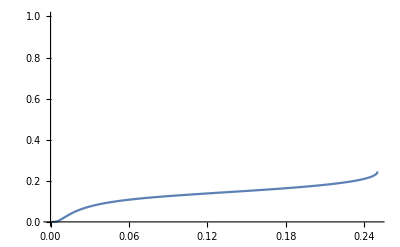

```mathematica
Plot[varFuncX[λ, 1.01]/sx^2, {λ, 0.001, 0.25}, PlotRange->{0, 1}]
```

```mathematica
ArrayPlot[meanArrayUncorrectedX, ColorFunction->(Blend[{{ 0,White},{1,Blue}},#]&), PlotLegends->{Placed[BarLegend[Automatic,None,LegendLabel->""],Right]}, FrameTicks->{xticks, yticks}, DataReversed->True, FrameLabel->{λ, x0}]
Grid[N[Reverse[meanArrayUncorrectedX],8]]
```

-Graphics-

0.723607 | 0.723607 | 0.723607 | 0.723607 | 0.723607 | 0.723607 | 0.723607 | 0.723607
0.887298 | 0.887298 | 0.887298 | 0.887298 | 0.887298 | 0.887298 | 0.887298 | 0.887298
0.947214 | 0.947214 | 0.947214 | 0.947214 | 0.947214 | 0.947214 | 0.947214 | 0.947214
0.979583 | 0.979583 | 0.979583 | 0.979583 | 0.979583 | 0.979583 | 0.979583 | 0.979583
0.989898 | 0.989898 | 0.989898 | 0.989898 | 0.989898 | 0.989898 | 0.989898 | 0.989898
0.994975 | 0.994975 | 0.994975 | 0.994975 | 0.994975 | 0.994975 | 0.994975 | 0.994975
0.997996 | 0.997996 | 0.997996 | 0.997996 | 0.997996 | 0.997996 | 0.997996 | 0.997996
0.998999 | 0.998999 | 0.998999 | 0.998999 | 0.998999 | 0.998999 | 0.998999 | 0.998999

```mathematica
ArrayPlot[meanArrayX/.sx->0.1, ColorFunction->(Blend[{{ 0,White},{1,Blue}},#]&), PlotLegends->{Placed[BarLegend[Automatic,None,LegendLabel->""],Right]}, FrameTicks->{xticks, yticks}, DataReversed->True, FrameLabel->{λ, x0}]
Grid[N[Reverse[meanArrayX/.sx->0.1],8]]
```

-Graphics-

0.716302 | 0.716402 | 0.716719 | 0.717275 | 0.718359 | 0.720706 | 0.722413 | 0.7233
0.868315 | 0.869111 | 0.871654 | 0.875645 | 0.881197 | 0.886361 | 0.887224 | 0.887296
0.907785 | 0.911941 | 0.923691 | 0.936346 | 0.944984 | 0.94718 | 0.947213 | 0.947214
0.89431 | 0.92087 | 0.96353 | 0.977881 | 0.979559 | 0.979583 | 0.979583 | 0.979583
0.872649 | 0.941171 | 0.986983 | 0.989869 | 0.989898 | 0.989898 | 0.989898 | 0.989898
0.898938 | 0.980817 | 0.99493 | 0.994975 | 0.994975 | 0.994975 | 0.994975 | 0.994975
0.98521 | 0.997902 | 0.997996 | 0.997996 | 0.997996 | 0.997996 | 0.997996 | 0.997996
0.998999 | 0.998999 | 0.998999 | 0.998999 | 0.998999 | 0.998999 | 0.998999 | 0.998999